## Some definitions first

```mathematica
IsRefinement[sets1_,sets2_]:=Block[{sets,result=False,merged},
sets=Subsets[sets2,{2}];
Table[
merged=Sort[Join[s[[1]],s[[2]]]];
If[MemberQ[sets1,merged],
result=True
(*Print["Not member",merged, " from ",sets1]*)
]
,
{s,sets}];
result
]
```

```mathematica
MobiusGraph[key_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[to[[1]],from[[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
MobiusTable[key_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars,result=Association[],set,level},
vars=ListofVars[form];
Table[
level=StringCount[SymbolName[n],"x"];
If[KeyExistsQ[result,level],
set=result[level],
set={}
];
set=Append[set,Coefficient[form,n]];
result[level]=set
,{n,vars}];
result
]
```

## Inequalities so we have pairs

```mathematica
ineqs=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

127

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqs2=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

127

```mathematica
ineqs2
```

{n1x2x3x4>0,-n12x3x4+n1x2x3x4>0,n123x4-n12x3x4-n13x2x4+n1x2x3x4>0,-n1234+n123x4+n124x3-n12x3x4+n134x2-n13x2x4-n14x2x3+n1x2x3x4>0,-2 n1234+2 n123x4+n124x3-n12x3x4+n134x2-n13x2x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4>0,-4 n1234+2 n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-6 n1234+2 n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4≥0,2 n1234-n12x34-n134x2-n1x234+n1x2x34>0,2 n1234-n124x3-n13x24-n1x234+n1x24x3≥0,-4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,n1234-n123x4-n14x23+n1x23x4>0,2 n1234-n123x4-n14x23-n1x234+n1x23x4>0,-n1234+n1x234>0,-2 n1234+n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4>0,-4 n1234+n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n124x3-n13x24+n1x24x3>0,-2 n1234+n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4-n14x2x3-n1x2x34+n1x2x3x4>0,n1234-n12x34-n134x2+n1x2x34>0,n1234-n124x3-n134x2+n14x2x3>0,2 n1234-n124x3-n134x2-n14x23+n14x2x3>0,-n1234+n14x23>0,2 n123x4-n12x3x4-n13x2x4-n1x23x4+n1x2x3x4>0,-2 n1234+2 n123x4+n124x3-n12x3x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+n134x2+n13x24-n13x2x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,-2 n1234+2 n123x4+n12x34-n12x3x4+n134x2-n13x2x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,-n123x4+n1x23x4>0,n1234-n123x4-n1x234+n1x23x4>0,-n1234+n123x4+n124x3-n12x3x4+n13x24-n13x2x4-n1x24x3+n1x2x3x4>0,-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n13x24-n13x2x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,-n1234+n123x4+n12x34-n12x3x4+n134x2-n13x2x4-n1x2x34+n1x2x3x4>0,-n123x4+n13x2x4>0,n1234-n123x4-n134x2+n13x2x4>0,2 n1234-n123x4-n134x2-n13x24+n13x2x4≥0,-n1234+n13x24≥0,-n1234+n134x2>0,n1234-n123x4-n13x24+n13x2x4>0,n124x3-n12x3x4-n14x2x3+n1x2x3x4>0,-n1234+n123x4+n124x3-n12x3x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4>0,-2 n1234+n123x4+2 n124x3-n12x3x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-4 n1234+n123x4+2 n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n124x3-n1x234+n1x24x3>0,-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,2 n124x3-n12x3x4-n14x2x3-n1x24x3+n1x2x3x4>0,-2 n1234+2 n124x3+n12x34-n12x3x4+n134x2-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,-n124x3+n1x24x3>0,-n1234+n124x3+n12x34-n12x3x4+n134x2-n14x2x3-n1x2x34+n1x2x3x4>0,-n124x3+n14x2x3>0,n1234-n124x3-n14x23+n14x2x3>0,n123x4-n12x3x4-n1x23x4+n1x2x3x4>0,-n1234+n123x4+n124x3-n12x3x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-2 n1234+n123x4+n124x3+n12x34-n12x3x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n12x34-n1x234+n1x2x34>0,-n1234+n123x4+n12x34-n12x3x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,n124x3-n12x3x4-n1x24x3+n1x2x3x4>0,-n1234+n124x3+n12x34-n12x3x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,n12x34-n12x3x4-n1x2x34+n1x2x3x4>0,-n12x34+n1x2x34>0,n12x3x4>0,-n123x4+n12x3x4>0,n1234-n123x4-n124x3+n12x3x4>0,2 n1234-n123x4-n124x3-n12x34+n12x3x4>0,-n1234+n12x34>0,-n1234+n124x3>0,n1234-n123x4-n12x34+n12x3x4>0,n123x4>0,-n1234+n123x4>0,n1234>0,-n124x3+n12x3x4>0,n1234-n124x3-n12x34+n12x3x4>0,n124x3>0,-n12x34+n12x3x4>0,n12x34>0,-n13x2x4+n1x2x3x4>0,n134x2-n13x2x4-n14x2x3+n1x2x3x4>0,-n1234+n123x4+n134x2-n13x2x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4>0,-3 n1234+n123x4+n124x3+n134x2+n13x24-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-4 n1234+n123x4+n124x3+2 n134x2+n13x24-n13x2x4+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n134x2-n1x234+n1x2x34>0,-2 n1234+n123x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,-n1234+n124x3+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4>0,-2 n1234+n124x3+2 n134x2+n13x24-n13x2x4-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,2 n134x2-n13x2x4-n14x2x3-n1x2x34+n1x2x3x4>0,-n134x2+n1x2x34>0,-n134x2+n14x2x3>0,n1234-n134x2-n14x23+n14x2x3>0,n123x4-n13x2x4-n1x23x4+n1x2x3x4>0,-n1234+n123x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-2 n1234+n123x4+n134x2+n13x24-n13x2x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n13x24-n1x234+n1x24x3>0,-n1234+n123x4+n134x2-n13x2x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,n13x24-n13x2x4-n1x24x3+n1x2x3x4>0,-n1234+n134x2+n13x24-n13x2x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,-n13x24+n1x24x3>0,n134x2-n13x2x4-n1x2x34+n1x2x3x4>0,n13x2x4>0,-n134x2+n13x2x4>0,n1234-n134x2-n13x24+n13x2x4>0,n134x2>0,-n13x24+n13x2x4>0,n13x24>0,-n14x2x3+n1x2x3x4>0,n14x23-n14x2x3-n1x23x4+n1x2x3x4>0,-n1234+n124x3+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-2 n1234+n124x3+n134x2+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,-n1234+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,-n14x23+n1x23x4>0,n1234-n14x23-n1x234+n1x23x4>0,n124x3-n14x2x3-n1x24x3+n1x2x3x4>0,-n1234+n124x3+n134x2-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,n134x2-n14x2x3-n1x2x34+n1x2x3x4>0,n14x2x3>0,-n14x23+n14x2x3>0,n14x23>0,-n1x23x4+n1x2x3x4>0,n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,-n1x234+n1x2x34>0,-n1x234+n1x24x3>0,n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,n1x23x4>0,-n1x234+n1x23x4>0,n1x234>0,-n1x24x3+n1x2x3x4>0,n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,n1x24x3>0,-n1x2x34+n1x2x3x4>0,n1x2x34>0}

```mathematica
realnullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofourrealnull"],0],{k,realyNullAtomKeys}];Length[realnullAtomFacts]
```

15

```mathematica
ineqsW2=Monitor[Simplify[Fold[And,Select[ineqs2,Length[ListofVars[#]]==2&]],Trig->False,ComplexityFunction->MyLeafCount],countDone];Length[ineqsW2]
```

31

```mathematica
Length[allGraphs]
```

127

```mathematica
allGraphs[9,"colofourrealnull"]
```

-n1x23x4+n1x2x3x4

```mathematica
vars2=Sort[DeleteDuplicates[ListofVars[Select[ineqsW2,Length[ListofVars[#]]==2&]]],BaseVarComp2]
```

{n1234,n1x234,n134x2,n124x3,n123x4,n14x23,n13x24,n12x34,n1x2x34,n1x24x3,n14x2x3,n1x23x4,n13x2x4,n12x3x4,n1x2x3x4}

```mathematica
InverseNull[symbol_]:=First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==symbol&]]
```

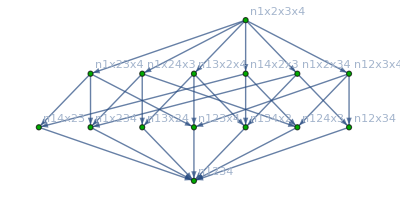

```mathematica
partialOrder=Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[k->Labeled[allGraphs[InverseNull[k],"graph"],k],{k,vars2}],GraphLayout->"LayeredDigraphEmbedding", VertexStyle->Table[k->ColourForKey[allGraphs,InverseNull[k]],{k,vars2}]]
```

```mathematica
EdgeCount[partialOrder]
```

31

```mathematica
VertexCount[partialOrder]
```

15

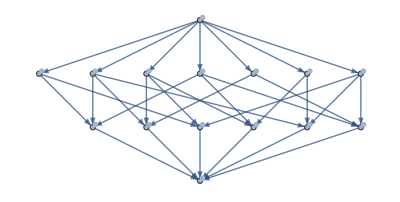

```mathematica
Graph[Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofourrealnull"]->allGraphs[k,"graph"],{k,realyNullAtomKeys}],MemberQ[vars2,#[[1]]]&]]
```

```mathematica
Take[ineqsW,5]
```

Take::normal: Nonatomic expression expected at position 1 in Take[ineqsW,5].

Take[ineqsW,5]

```mathematica
pairs=Subsets[nullAtomSymbols,{2}];Length[pairs]
```

105

```mathematica
Take[nullAtomFacts,3]
```

{p1x2x3x4>0,p1x2x34>0,p1x24x3>0}

```mathematica
atomFactsAnd=Fold[And,nullAtomFacts]
```

p1x2x3x4>0&&p1x2x34>0&&p1x24x3>0&&p1x23x4>0&&p1x234>0&&p14x2x3>0&&p14x23>0&&p13x2x4>0&&p13x24>0&&p134x2>0&&p12x3x4>0&&p12x34>0&&p124x3>0&&p123x4>0&&p1234≥0

```mathematica
allGraphs[6562,"graph"]
```

Missing[KeyAbsent,6562]

## Mobius and zeta

```mathematica
allVars=Sort[DeleteDuplicates[ListofVars[ineqsW2]]];
```

```mathematica
vertices=Sort[Sort[allVars],BaseVarComp2]
```

{n1234,n1x234,n134x2,n124x3,n123x4,n14x23,n13x24,n12x34,n1x2x34,n1x24x3,n1x23x4,n14x2x3,n13x2x4,n12x3x4,n1x2x3x4}

```mathematica
(*vertices=Table[allGraphs[k,"colofourrealnull"],{k,Reverse[realyNullAtomKeys]}];Length[vertices]*)
```

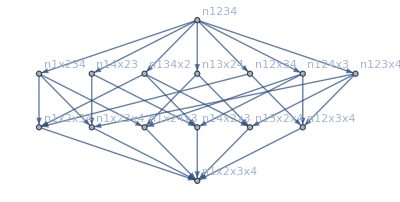

```mathematica
four=Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
fourM[[2,9]]==1&&fourM[[2,10]]==1&&fourM[[2,11]]==1
```

Part::partd: Part specification fourM⟦2,9⟧ is longer than depth of object.

Part::partd: Part specification fourM⟦2,10⟧ is longer than depth of object.

Part::partd: Part specification fourM⟦2,11⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

fourM⟦2,9⟧==1&&fourM⟦2,10⟧==1&&fourM⟦2,11⟧==1

```mathematica
fourM[[5,14]]
```

Part::partd: Part specification fourM⟦5,14⟧ is longer than depth of object.

fourM⟦5,14⟧

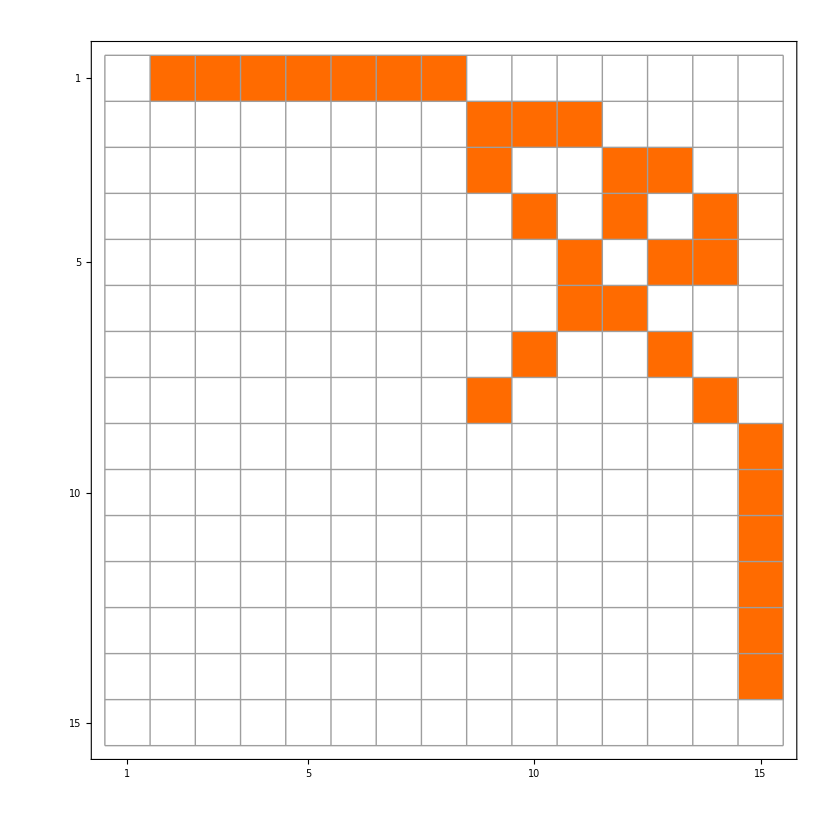

```mathematica
fourM=AdjacencyMatrix[four];MatrixPlot[fourM,Mesh->All]
```

## This is enough

```mathematica
IM=IdentityMatrix[Length[VertexList[four]]];
```

```mathematica
MakeOne[mat_]:=Map[Map[If[#!=0,1,0]&,#]&, mat]
```

```mathematica
ZetaM=MakeOne[Inverse[IM-fourM]];MatrixForm[ZetaM]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MobiusM=Inverse[ZetaM];MatrixForm[MobiusM,TableHeadings->{VertexList[four],Map[Rotate[#,-Pi/2]&, VertexList[four]]}]
```

( | n1234 | n1x234 | n134x2 | n124x3 | n123x4 | n14x23 | n13x24 | n12x34 | n1x2x34 | n1x24x3 | n1x23x4 | n14x2x3 | n13x2x4 | n12x3x4 | n1x2x3x4
n1234 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2 | 2 | 2 | 2 | 2 | 2 | -6
n1x234 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 2
n134x2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 2
n124x3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 2
n123x4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 2
n14x23 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1
n13x24 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 1
n12x34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 1
n1x2x34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
n1x24x3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
n1x23x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
n14x2x3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
n13x2x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
n12x3x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
n1x2x3x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Det[MobiusM]
```

1

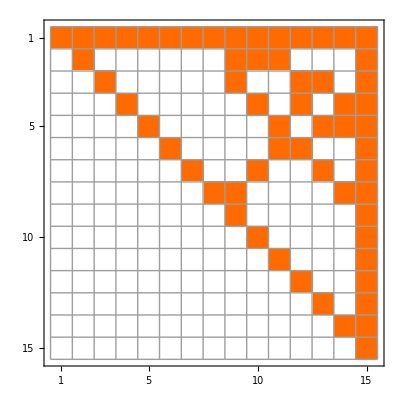

```mathematica
MatrixPlot[ZetaM,Mesh->All]
```

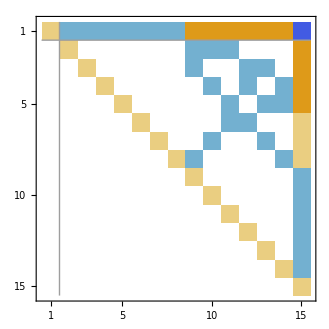

```mathematica
MatrixPlot[MobiusM,Mesh->{Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}],Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}]}]
```

```mathematica
Mob=Association[]
```

<||>

```mathematica
Length[VertexList[four]]
```

15

```mathematica
MobiusM[[5]]
```

{0,0,0,0,1,0,0,0,0,0,-1,0,-1,-1,2}

```mathematica
With[{l=VertexList[four]},
Table[Mob[l[[k]]]=MobiusM[[Length[l],k]],{k,1,Length[l]}]
]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
Gr=Association[];With[{l=VertexList[four]},
Table[Gr[l[[k]]]=allGraphs[First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==l[[k]]&]],"vertexsets"],{k,1,Length[l]}]
]
```

{{{1,2,3,4}},{{1},{2,3,4}},{{1,3,4},{2}},{{1,2,4},{3}},{{1,2,3},{4}},{{1,4},{2,3}},{{1,3},{2,4}},{{1,2},{3,4}},{{1},{2},{3,4}},{{1},{2,4},{3}},{{1},{2,3},{4}},{{1,4},{2},{3}},{{1,3},{2},{4}},{{1,2},{3},{4}},{{1},{2},{3},{4}}}

```mathematica
Gr2=Association[];With[{l=VertexList[four]},
Table[Gr2[l[[k]]]=allGraphs[First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==l[[k]]&]]],{k,1,Length[l]}]
];
```

```mathematica
Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->Rotate[ToString[Gr[v]],Pi/4]->Mob[v],{v,VertexList[four]}],GraphLayout->"TutteEmbedding",DirectedEdges->False]
```

```mathematica
Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->Mob[v],{v,VertexList[four]}],GraphLayout->"TutteEmbedding",DirectedEdges->False]
```

```mathematica
Take[Table[{Gr2[v,"graph"],v,Gr[v],Mob[v],4^Length[Gr[v]],FactorInteger[Mob[v]*4^Length[Gr[v]]]},{v,VertexList[four]}],3]
```

{{-Graphics-,n1234,{{1,2,3,4}},0,4,{{0,1}}},{-Graphics-,n1x234,{{1},{2,3,4}},0,16,{{0,1}}},{-Graphics-,n134x2,{{1,3,4},{2}},0,16,{{0,1}}}}

```mathematica
TableForm[Sort[Table[{Gr2[v,"graph"],v,Gr[v],Mob[v],4^Length[Gr[v]],Mob[v]*4^Length[Gr[v]],FactorInteger[Mob[v]*4^Length[Gr[v]]]},{v,VertexList[four]}],Abs[#1[[4]]]>Abs[#2[[4]]]&],TableDepth->2]
```

-Graphics- | n1x2x3x4 | {{1},{2},{3},{4}} | 1 | 256 | 256 | {{2,8}}
-Graphics- | n12x3x4 | {{1,2},{3},{4}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n13x2x4 | {{1,3},{2},{4}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n14x2x3 | {{1,4},{2},{3}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n1x23x4 | {{1},{2,3},{4}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n1x24x3 | {{1},{2,4},{3}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n1x2x34 | {{1},{2},{3,4}} | 0 | 64 | 0 | {{0,1}}
-Graphics- | n12x34 | {{1,2},{3,4}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n13x24 | {{1,3},{2,4}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n14x23 | {{1,4},{2,3}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n123x4 | {{1,2,3},{4}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n124x3 | {{1,2,4},{3}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n134x2 | {{1,3,4},{2}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n1x234 | {{1},{2,3,4}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n1234 | {{1,2,3,4}} | 0 | 4 | 0 | {{0,1}}

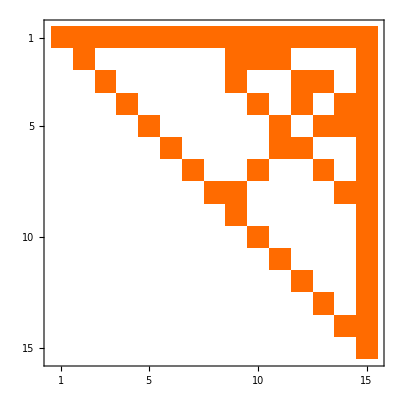

```mathematica
ZetaM//MatrixPlot
```

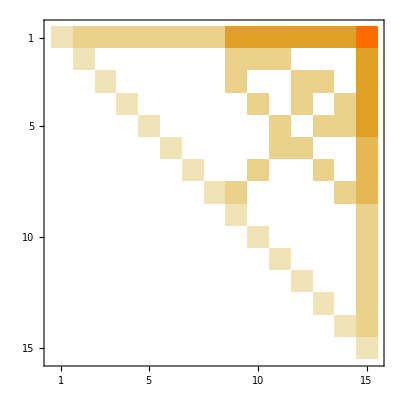

```mathematica
MatrixPower[ZetaM,2]//MatrixPlot
```

```mathematica
Table[MatrixPower[ZetaM,k]//MatrixForm,{k,0,10}]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 5 | 5 | 5 | 5 | 5 | 5 | 15
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 5
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 2 | 0 | 5
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 5
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 5
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 2 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 12 | 12 | 12 | 12 | 12 | 12 | 60
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 12
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 3 | 0 | 12
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 0 | 3 | 12
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 3 | 3 | 12
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 0 | 0 | 0 | 0 | 3 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 22 | 22 | 22 | 22 | 22 | 22 | 154
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 4 | 0 | 0 | 0 | 22
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 4 | 4 | 0 | 22
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 0 | 4 | 22
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 4 | 22
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 16
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 4 | 0 | 16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 0 | 0 | 0 | 0 | 4 | 16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 35 | 35 | 35 | 35 | 35 | 35 | 315
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 5 | 0 | 0 | 0 | 35
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 5 | 5 | 0 | 35
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 5 | 0 | 5 | 35
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 5 | 5 | 35
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 25
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 5 | 0 | 0 | 5 | 0 | 25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 5 | 0 | 0 | 0 | 0 | 5 | 25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 51 | 51 | 51 | 51 | 51 | 51 | 561
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 6 | 6 | 0 | 0 | 0 | 51
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 6 | 0 | 51
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 0 | 6 | 51
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 6 | 51
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 6 | 6 | 0 | 0 | 36
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 36
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 6 | 0 | 0 | 0 | 0 | 6 | 36
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 70 | 70 | 70 | 70 | 70 | 70 | 910
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 7 | 7 | 0 | 0 | 0 | 70
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 7 | 7 | 0 | 70
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 7 | 0 | 7 | 70
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 7 | 7 | 70
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 7 | 7 | 0 | 0 | 49
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 7 | 0 | 0 | 7 | 0 | 49
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 0 | 0 | 0 | 0 | 7 | 49
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 92 | 92 | 92 | 92 | 92 | 92 | 1380
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 8 | 8 | 0 | 0 | 0 | 92
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 8 | 8 | 0 | 92
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 8 | 0 | 8 | 92
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 8 | 8 | 92
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 8 | 8 | 0 | 0 | 64
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 8 | 0 | 0 | 8 | 0 | 64
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8 | 0 | 0 | 0 | 0 | 8 | 64
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 117 | 117 | 117 | 117 | 117 | 117 | 1989
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 9 | 9 | 0 | 0 | 0 | 117
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 9 | 9 | 0 | 117
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 9 | 0 | 9 | 117
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 9 | 9 | 117
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 9 | 9 | 0 | 0 | 81
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 9 | 0 | 0 | 9 | 0 | 81
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 9 | 0 | 0 | 0 | 0 | 9 | 81
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 145 | 145 | 145 | 145 | 145 | 145 | 2755
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 10 | 10 | 0 | 0 | 0 | 145
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 10 | 10 | 0 | 145
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 10 | 0 | 10 | 145
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 10 | 10 | 145
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 10 | 10 | 0 | 0 | 100
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 10 | 0 | 0 | 10 | 0 | 100
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 10 | 0 | 0 | 0 | 0 | 10 | 100
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
Table[MatrixPower[MobiusM,k]//MatrixForm,{k,0,10}]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2 | 2 | 2 | 2 | 2 | 2 | -6
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 2
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 2
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 2
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 2
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -2 | -2 | -2 | -2 | -2 | -2 | -2 | 7 | 7 | 7 | 7 | 7 | 7 | -35
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | -2 | 0 | 0 | 0 | 7
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | -2 | 0 | 7
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | -2 | 0 | -2 | 7
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | -2 | -2 | 7
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -2 | -2 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 0 | 0 | 0 | 0 | -2 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -3 | -3 | -3 | -3 | -3 | -3 | -3 | 15 | 15 | 15 | 15 | 15 | 15 | -105
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | -3 | -3 | 0 | 0 | 0 | 15
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | -3 | -3 | 0 | 15
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -3 | 0 | -3 | 0 | -3 | 15
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -3 | 0 | -3 | -3 | 15
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -3 | -3 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -3 | 0 | 0 | -3 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -3 | 0 | 0 | 0 | 0 | -3 | 9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -4 | -4 | -4 | -4 | -4 | -4 | -4 | 26 | 26 | 26 | 26 | 26 | 26 | -234
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | -4 | 0 | 0 | 0 | 26
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | -4 | -4 | 0 | 26
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | -4 | 0 | -4 | 26
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | -4 | -4 | 26
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -4 | -4 | 0 | 0 | 16
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -4 | 0 | 0 | -4 | 0 | 16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4 | 0 | 0 | 0 | 0 | -4 | 16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 40 | 40 | 40 | 40 | 40 | 40 | -440
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | -5 | 0 | 0 | 0 | 40
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -5 | 0 | 0 | -5 | -5 | 0 | 40
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -5 | 0 | -5 | 0 | -5 | 40
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -5 | 0 | -5 | -5 | 40
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -5 | -5 | 0 | 0 | 25
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -5 | 0 | 0 | -5 | 0 | 25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | 0 | 0 | 0 | 0 | -5 | 25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -6 | -6 | -6 | -6 | -6 | -6 | -6 | 57 | 57 | 57 | 57 | 57 | 57 | -741
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -6 | -6 | -6 | 0 | 0 | 0 | 57
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -6 | 0 | 0 | -6 | -6 | 0 | 57
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -6 | 0 | -6 | 0 | -6 | 57
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -6 | 0 | -6 | -6 | 57
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -6 | -6 | 0 | 0 | 36
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -6 | 0 | 0 | -6 | 0 | 36
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -6 | 0 | 0 | 0 | 0 | -6 | 36
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -7 | -7 | -7 | -7 | -7 | -7 | -7 | 77 | 77 | 77 | 77 | 77 | 77 | -1155
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -7 | -7 | -7 | 0 | 0 | 0 | 77
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -7 | 0 | 0 | -7 | -7 | 0 | 77
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -7 | 0 | -7 | 0 | -7 | 77
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -7 | 0 | -7 | -7 | 77
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -7 | -7 | 0 | 0 | 49
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -7 | 0 | 0 | -7 | 0 | 49
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -7 | 0 | 0 | 0 | 0 | -7 | 49
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -8 | -8 | -8 | -8 | -8 | -8 | -8 | 100 | 100 | 100 | 100 | 100 | 100 | -1700
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -8 | -8 | -8 | 0 | 0 | 0 | 100
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -8 | 0 | 0 | -8 | -8 | 0 | 100
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -8 | 0 | -8 | 0 | -8 | 100
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -8 | 0 | -8 | -8 | 100
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -8 | -8 | 0 | 0 | 64
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -8 | 0 | 0 | -8 | 0 | 64
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -8 | 0 | 0 | 0 | 0 | -8 | 64
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -9 | -9 | -9 | -9 | -9 | -9 | -9 | 126 | 126 | 126 | 126 | 126 | 126 | -2394
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -9 | -9 | -9 | 0 | 0 | 0 | 126
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -9 | 0 | 0 | -9 | -9 | 0 | 126
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -9 | 0 | -9 | 0 | -9 | 126
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -9 | 0 | -9 | -9 | 126
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -9 | -9 | 0 | 0 | 81
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -9 | 0 | 0 | -9 | 0 | 81
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -9 | 0 | 0 | 0 | 0 | -9 | 81
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | -10 | -10 | -10 | -10 | -10 | -10 | -10 | 155 | 155 | 155 | 155 | 155 | 155 | -3255
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -10 | -10 | -10 | 0 | 0 | 0 | 155
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -10 | 0 | 0 | -10 | -10 | 0 | 155
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -10 | 0 | -10 | 0 | -10 | 155
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -10 | 0 | -10 | -10 | 155
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -10 | -10 | 0 | 0 | 100
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -10 | 0 | 0 | -10 | 0 | 100
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -10 | 0 | 0 | 0 | 0 | -10 | 100
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

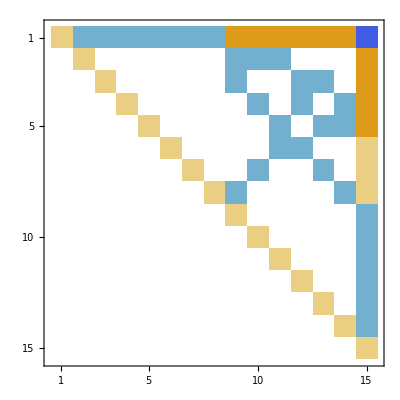

```mathematica
Inverse[ZetaM]//MatrixPlot
```

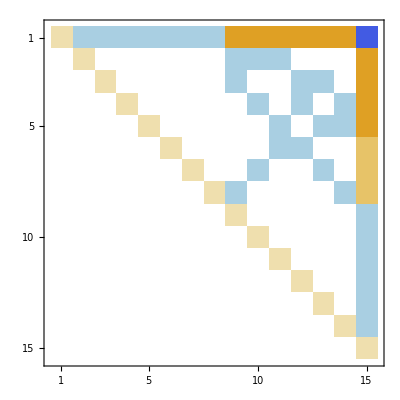

```mathematica
MatrixPower[Inverse[ZetaM],3]//MatrixPlot
```

```mathematica
MatrixPower[Inverse[ZetaM],15]//MatrixForm
```

(1 | -15 | -15 | -15 | -15 | -15 | -15 | -15 | 345 | 345 | 345 | 345 | 345 | 345 | -10695
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -15 | -15 | -15 | 0 | 0 | 0 | 345
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -15 | 0 | 0 | -15 | -15 | 0 | 345
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -15 | 0 | -15 | 0 | -15 | 345
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -15 | 0 | -15 | -15 | 345
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -15 | -15 | 0 | 0 | 225
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -15 | 0 | 0 | -15 | 0 | 225
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -15 | 0 | 0 | 0 | 0 | -15 | 225
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Subgraph
```

Subgraph

```mathematica
GraphZeta[g_]:=Block[{ordered=TopologicalSort[four]},
Table[If[ToString[i]==ToString[j]||EdgeQ[g,i->j],1,0],{i,ordered},{j,ordered}]
]
```

```mathematica
GraphZeta[four]//MatrixForm
```

(1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Inverse[GraphZeta[four]]//MatrixForm
```

(1 | -1 | -1 | -1 | 3 | -1 | -1 | 3 | -1 | 3 | -1 | 3 | 3 | 3 | -18
0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 3
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 3
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MobiusTable[13]
```

<|3→{1},1→{2},2→{-1,-1,-1}|>